### FINDING EFFECITVE α

```mathematica
(* On this notebook I examine the possibilities of having an effective alpha that encodes the effect of the dissipation kappa*)
```

```mathematica
f[α_]:=1/72 ⅇ^(-α^2) (72-288 α^2+276 α^4-128 α^6+25 α^8-2 α^10);
eqn[x_,α_,κ_]:=4+12 f[α] (1-κ)-3 κ==4+12 f[x];
```

```mathematica
(*Parameter ranges*)
alphaVals=Range[0.,1,0.01];
kappaVals=Range[0.,1,0.01];
nA=Length[alphaVals];
nK=Length[kappaVals];
data1=ConstantArray[0.,{nA,nK}];
Do[a=alphaVals[[i]];k=kappaVals[[j]];
x0=If[j==1 || (a<=0.7 && k <=0.7), Sqrt[a^2+(1/4-a^2) k],data1[[i,j-1]]];
sol=FindRoot[eqn[x,a,k],{x,x0}];
data1[[i,j]]=x/. sol; ,{i,1,nA},{j,1,nK}];
flattenedAKX=Flatten[Table[{alphaVals[[i]],kappaVals[[j]],data1[[i,j]]},{i,Length[alphaVals]},{j,Length[kappaVals]}],1]; (*exact solution*)
```

Now I plot the heat map of the effective kappa and alpha.

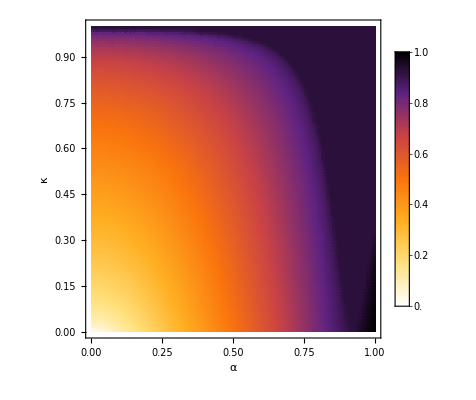

```mathematica
ListDensityPlot[flattenedAKX,FrameLabel->{"α","κ"},ColorFunction->ColorData[{"SunsetColors","Reverse"}],PlotLegends->Automatic, InterpolationOrder->2,PlotRange->All,LabelStyle->Directive[FontSize->14]]
```

Let us compute now the difference on fidelities. When considering this, there is a curse of dimensionality.

```mathematica
fiddis[L_,t_,α_,κ_]:=1/2^L(1+(((4+12f[α](1-κ)-3κ)^(L/2)-1)/(4^L-1))^t(2^L-1));
fid[L_,t_,α_]:=1/2^L(1+(((4+12f[α])^(L/2)-1)/(4^L-1))^t(2^L-1));
```

```mathematica
DeltaFid[L_,t_]:= Table[{flattenedAKX[[i,1]],flattenedAKX[[i,2]],Abs[fiddis[L,t,flattenedAKX[[i,1]],flattenedAKX[[i,2]]]-fid[L,t,flattenedAKX[[i,3]]]]},{i,Length[flattenedAKX]}]
```

For 8 probably I have numerical issues.

Hence, it is much visual to compare the core of the equation, removing all dependence on time and number of qubits.

```mathematica
Coredis[α_,κ_]:=4+12 f[α] (1-κ)-3 κ;
Core[α_]:=4+12 f[α]
DeltaCores=Table[{flattenedAKX[[i,1]],flattenedAKX[[i,2]],Abs[Coredis[flattenedAKX[[i,1]],flattenedAKX[[i,2]]]-Core[flattenedAKX[[i,3]]]]},{i,Length[flattenedAKX]}];
```

```mathematica
ListDensityPlot[DeltaCores,FrameLabel->{"α","κ"},ColorFunction->ColorData[{"SunsetColors","Reverse"}],PlotLegends->Automatic, InterpolationOrder->2,PlotRange->All,LabelStyle->Directive[FontSize->14]]
```

```mathematica
(*Parameter ranges*)
alphaVals=Range[0.,1,0.001];
kappaVals=Range[0.,1,0.001];
nA=Length[alphaVals];
nK=Length[kappaVals];
data1=ConstantArray[0.,{nA,nK}];
(*choose a high recursion limit*)
maxRec=10000;

Do[a=alphaVals[[i]];
k=kappaVals[[j]];
x0=If[j==1||(a<=0.7&&k<=0.7),Sqrt[a^2+(1/4-a^2) k],0.8];
(*locally raise the recursion limit for this FindRoot*)solRule=Block[{RecursionLimit=maxRec},Check[FindRoot[eqn[x,a,k],{x,x0}],(*on any FindRoot failure*){x->-1}]];
data1[[i,j]]=x/. solRule;,{i,1,nA},{j,1,nK}];

flattenedAKX1=Flatten[Table[{alphaVals[[i]],kappaVals[[j]],data1[[i,j]]},{i,Length[alphaVals]},{j,Length[kappaVals]}],1];
```

```mathematica
zMin=0;
zMax=1;

plt=ListDensityPlot[flattenedAKX1,FrameLabel->{"α","κ"},InterpolationOrder->2,PlotRange->All,LabelStyle->Directive[FontSize->14],(*disable auto‑scaling so “#” is the raw z value*)ColorFunctionScaling->False,(*single-argument function for density plots*)ColorFunction->Function[{z},If[z<zMin,(*everything below 0 gets gray*)GrayLevel[0.85],(*everything 0–1 gets the reversed-Sunset ramp*)ColorData[{"SunsetColors","Reverse"}][Rescale[z,{zMin,zMax}]]]],(*manually build a legend only for[0,1]*)PlotLegends->BarLegend[{ColorData[{"SunsetColors","Reverse"}],{0,1}},LegendLabel->Style[Subscript[α,"eff"],14],LabelStyle->Directive[FontSize->12]]]
```

## EFFECTIVE KAPPA

```mathematica
fidonlykappa[L_,t_,κ_]:=1/2^L(1+(((16-15κ)^(L/2)-1)/(4^L-1))^t(2^L-1));
kappaeff[α_,κ_]=1/15(12(1- f[α](1-κ))+3κ);
```

```mathematica
alphaVals=Range[0.,1,0.01];
kappaVals=Range[0.,1,0.01];
```

```mathematica
datakappas=Table[kappaeff[α,κ],{α,alphaVals},{κ,kappaVals}];
flattenedkappa=Flatten[Table[{alphaVals[[i]],kappaVals[[j]],datakappas[[i,j]]},{i,Length[alphaVals]},{j,Length[kappaVals]}],1];
```

```mathematica
DeltaFidkappa[L_,t_]:= Table[{flattenedkappa[[i,1]],flattenedkappa[[i,2]],Abs[fiddis[L,t,flattenedkappa[[i,1]],flattenedkappa[[i,2]]]-fidonlykappa[L,t,flattenedkappa[[i,3]]]]},{i,Length[flattenedkappa]}]
```

```mathematica
pltkappa=ListDensityPlot[flattenedkappa,FrameLabel->{"α","κ"},
InterpolationOrder->2,PlotRange->All,
LabelStyle->Directive[FontSize->14],
ColorFunction->ColorData[{"SunsetColors","Reverse"}],PlotLegends->BarLegend[{ColorData[{"SunsetColors","Reverse"}],{0,1}},
LegendLabel->Style[Subscript[κ,"eff"],14],
LabelStyle->Directive[FontSize->12]]]
```